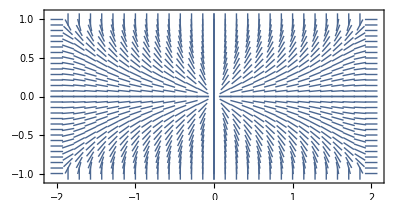

```mathematica
sol1=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==π/2,A[2,y]==0,A[x,0]==0,A[x,1]==π/2},{A[x,y]},{x,0,2},{y,0,1}];
s1=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol1],{x,0,2},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/2];
sol2=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==π,A[0,y]==π/2,A[x,0]==π,A[x,1]==π/2},{A[x,y]},{x,-2,0},{y,0,1}];
s2=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol2],{x,-2,0},{y,0,1}, VectorStyle->{ Arrowheads[0]},AspectRatio->1/2];
sol3=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==-π/2,A[2,y]==0,A[x,0]==0,A[x,-1]==-π/2},{A[x,y]},{x,0,2},{y,-1,0}];
s3=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol3],{x,0,2},{y,-1,0} ,VectorStyle->{Arrowheads[0]},AspectRatio->1/2];
sol4=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==-π,A[0,y]==-π/2,A[x,0]==-π,A[x,-1]==-π/2},{A[x,y]},{x,-2,0},{y,-1,0}];
s4=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol4],{x,-2,0},{y,-1,0} ,VectorStyle->{ Arrowheads[0]},AspectRatio->1/2];
Show[s1,s2,s3,s4,PlotRange->All]
```

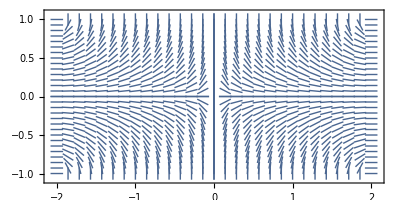

```mathematica
sol5=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==-π/2,A[2,y]==0,A[x,0]==0,A[x,1]==-π/2},{A[x,y]},{x,0,2},{y,0,1}];
s5=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol5],{x,0,2},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/2];
sol6=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==-π,A[0,y]==-π/2,A[x,0]==-π,A[x,1]==-π/2},{A[x,y]},{x,-2,0},{y,0,1}];
s6=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol6],{x,-2,0},{y,0,1}, VectorStyle->{ Arrowheads[0]},AspectRatio->1/2];
sol7=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==π/2,A[2,y]==0,A[x,0]==0,A[x,-1]==π/2},{A[x,y]},{x,0,2},{y,-1,0}];
s7=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol7],{x,0,2},{y,-1,0} ,VectorStyle->{Arrowheads[0]},AspectRatio->1/2];
sol8=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==π,A[0,y]==π/2,A[x,0]==π,A[x,-1]==π/2},{A[x,y]},{x,-2,0},{y,-1,0}];
s8=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol8],{x,-2,0},{y,-1,0} ,VectorStyle->{ Arrowheads[0]},AspectRatio->1/2];
Show[s5,s6,s7,s8,PlotRange->All]
```

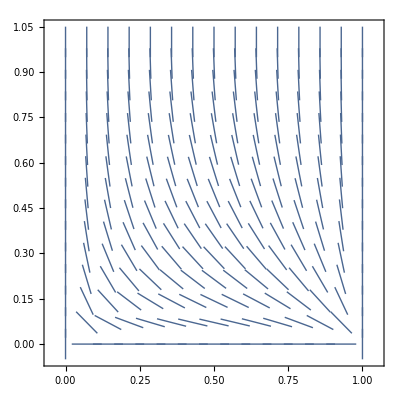

```mathematica
sol9=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==-π/2,A[1,y]==-π/2,A[x,0]==0,A[x,1]==-π/2},{A[x,y]},{x,0,1},{y,0,1}];
s9=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol9],{x,0,1},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/1]
```

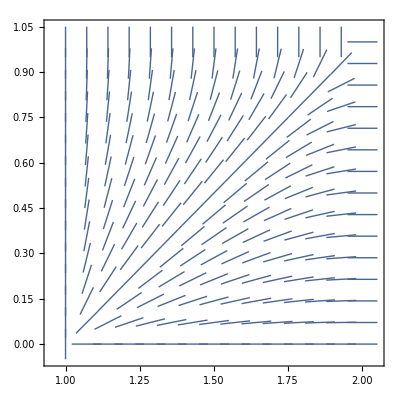

```mathematica
sol10=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[1,y]==-π/2,A[2,y]==-π,A[x,0]==-π,A[x,1]==-π/2},{A[x,y]},{x,1,2},{y,0,1}];
s10=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol10],{x,1,2},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/1]
```

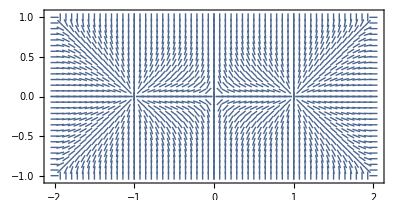

```mathematica
sol11=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==-π/2,A[0,y]==-π/2,A[x,0]==-π,A[x,1]==-π/2},{A[x,y]},{x,-1,0},{y,0,1}];
s11=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol11],{x,-1,0},{y,0,1}, VectorStyle->{ Arrowheads[0]}];
sol12=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==-π/2,A[-2,y]==0,A[x,0]==0,A[x,1]==-π/2},{A[x,y]},{x,-2,-1},{y,0,1}];
s12=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol12],{x,-2,-1},{y,0,1}, VectorStyle->{ Arrowheads[0]}];
sol13=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==π/2,A[1,y]==π/2,A[x,0]==0,A[x,-1]==π/2},{A[x,y]},{x,0,1},{y,-1,0}];
s13=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol13],{x,0,1},{y,-1,0} ,VectorStyle->{Arrowheads[0]}];
sol14=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[1,y]==π/2,A[2,y]==π,A[x,0]==π,A[x,-1]==π/2},{A[x,y]},{x,1,2},{y,-1,0}];
s14=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol14],{x,1,2},{y,-1,0} ,VectorStyle->{Arrowheads[0]}];
sol15=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==π/2,A[0,y]==π/2,A[x,0]==π,A[x,-1]==π/2},{A[x,y]},{x,-1,0},{y,-1,0}];
s15=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol15],{x,-1,0},{y,-1,0} ,VectorStyle->{ Arrowheads[0]}];
sol16=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==0,A[-1,y]==π/2,A[x,0]==0,A[x,-1]==π/2},{A[x,y]},{x,-2,-1},{y,-1,0}];
s16=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol16],{x,-2,-1},{y,-1,0} ,VectorStyle->{ Arrowheads[0]}];
Show[s9,s10,s11,s12,s13,s14,s15,s16,PlotRange->All,AspectRatio->1/2]
```

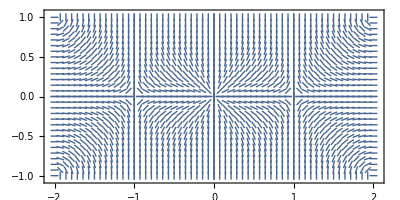

```mathematica
sol17=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==π/2,A[0,y]==π/2,A[x,0]==π,A[x,1]==π/2},{A[x,y]},{x,-1,0},{y,0,1}];
s17=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol17],{x,-1,0},{y,0,1}, VectorStyle->{ Arrowheads[0]}];
sol18=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==π/2,A[-2,y]==0,A[x,0]==0,A[x,1]==π/2},{A[x,y]},{x,-2,-1},{y,0,1}];
s18=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol18],{x,-2,-1},{y,0,1}, VectorStyle->{ Arrowheads[0]}];
sol19=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==-π/2,A[1,y]==-π/2,A[x,0]==0,A[x,-1]==-π/2},{A[x,y]},{x,0,1},{y,-1,0}];
s19=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol19],{x,0,1},{y,-1,0} ,VectorStyle->{Arrowheads[0]}];
sol20=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[1,y]==-π/2,A[2,y]==-π,A[x,0]==-π,A[x,-1]==-π/2},{A[x,y]},{x,1,2},{y,-1,0}];
s20=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol20],{x,1,2},{y,-1,0} ,VectorStyle->{Arrowheads[0]}];
sol21=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-1,y]==-π/2,A[0,y]==-π/2,A[x,0]==-π,A[x,-1]==-π/2},{A[x,y]},{x,-1,0},{y,-1,0}];
s21=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol21],{x,-1,0},{y,-1,0} ,VectorStyle->{ Arrowheads[0]}];
sol22=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[-2,y]==0,A[-1,y]==-π/2,A[x,0]==0,A[x,-1]==-π/2},{A[x,y]},{x,-2,-1},{y,-1,0}];
s22=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol22],{x,-2,-1},{y,-1,0} ,VectorStyle->{ Arrowheads[0]}];
sol23=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[0,y]==π/2,A[1,y]==π/2,A[x,0]==0,A[x,1]==π/2},{A[x,y]},{x,0,1},{y,0,1}];
s23=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol23],{x,0,1},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/1];
sol24=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]==0,A[1,y]==π/2,A[2,y]==π,A[x,0]==π,A[x,1]==π/2},{A[x,y]},{x,1,2},{y,0,1}];
s24=VectorPlot[Evaluate[{Cos[A[x,y]],Sin[A[x,y]]}/.sol24],{x,1,2},{y,0,1} ,VectorStyle->Arrowheads[0],AspectRatio->1/1];
Show[s17,s18,s19,s20,s21,s22,s23,s24,PlotRange->All,AspectRatio->1/2]
```